```mathematica
Exit[]
```

#### Utilities & Colors

```mathematica
Comb1={RGBColor["#206a5d"],RGBColor["#81b214"],RGBColor["#ffcc29"],RGBColor["#f58634"]};
Comb2={RGBColor["#d92027"],RGBColor["#ff9234"],RGBColor["#ffcd3c"],RGBColor["#35d0ba"]};
Comb3={RGBColor["#252525"],RGBColor["#6930c3"],RGBColor["#64dfdf"],RGBColor["#80ffdb"]};
Comb4={RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#40a8c4"],RGBColor["#a2d5f2"]};
Comb5={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
Comb6={RGBColor["#40a8c4"],RGBColor["#ffc93c"],RGBColor["#07689f"],RGBColor["#a2d5f2"]};
leg[label_,dim_,α_,x_,y_,col_]:=Inset[Rotate[Style[label,dim,col,FontFamily->"Palatino"],α Degree],Scaled[{x,y}]]
```

# QNMs of Halo Black Holes

```mathematica
(*Quit*)
```

```mathematica
(* non grid-based interpolation scheme to calculate QNMs of Schwarzschild black holes, I may have modified their method a bit. 
A HUGE CAUTION: any number you use has to be Rationalized or for large amount of grid points the code fail to work due to the differentiation matrices obtaining zero values*)
(* Main method taken from [arxiv:1610.08135v4] *)
```

```mathematica
SetDirectory[NotebookDirectory[]];
path=SetDirectory[NotebookDirectory[]];
```

```mathematica
<<HaloFlux`
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
n=19;
```

## Setting up the Matrix Method

### Wave equation

#### Master equation

```mathematica
h[r_]=(1-2m[r]/r);
```

```mathematica
V[r_]:=f[r]((l(l+1))/r^2-(6 m[r])/r^3+m'[r]/r^2);
```

```mathematica
eq=-r^3 ( ( ω^2-V[r])ϕ[r]+(h[r] f'[r]+f[r] h'[r])/2 ϕ'[r]+f[r] h[r] ϕ''[r])//.{f'[r]->(2 f[r] m[r])/(r (r-2 m[r]))}//Simplify
```

ϕ[r] (-r^3 ω^2+f[r] (-6 m[r]+r (l+l^2+m'[r])))+r f[r] (-2 m[r] (ϕ'[r]-r ϕ''[r])+r (m'[r] ϕ'[r]-r ϕ''[r]))

#### Change of coordinates

```mathematica
rn=r/.Solve[x==(1-rh/r),{r}][[1]];
dxr=D[(1-rh/r),r]/.r->rn;
ddxr=D[(1-rh/r),{r,2}]/.r->rn;
```

```mathematica
eqx= eq/.{r->rn,ϕ[r]->ϕ[x],ϕ'[r]->ϕ'[x]dxr,ϕ''[r]-> (dxr)^2 ϕ''[x]+ddxr*ϕ'[x]}//Collect[#,_[x],Simplify]&
```

ϕ[x] ((rh^3 ω^2)/(-1+x)^3+f[-rh/(-1+x)] (-6 m[-rh/(-1+x)]-(rh (l+l^2+m'[-rh/(-1+x)]))/(-1+x)))+f[-rh/(-1+x)] (6 (-1+x) m[-rh/(-1+x)]+rh (2+m'[-rh/(-1+x)])) ϕ'[x]+(-1+x) f[-rh/(-1+x)] (rh+2 (-1+x) m[-rh/(-1+x)]) ϕ''[x]

### Boundary conditions

#### Horizon

```mathematica
(*The substitutions in this case regard the properties of the functions f and m in the case of generic halo. m[rh] is always equal to rh/2, m'[rh] is always null. Then, I put f[rh]=0*) 
$Assumptions={l≥0,ri>0,rh>ri,l∈Integers};
ϕDiv[x_]:=(x)^p
Series[1/ϕDiv[x]eqx/.{ϕ->(ϕDiv[#]&)}//Simplify,{x,0,0}]
```

-((-1+p) p f[rh] (rh-2 m[rh]))/x^2+1/x(p f[rh] (-6 m[rh]+rh (2+m'[rh]))+(-1+p) p ((rh-2 m[rh]) (f[rh]-rh f'[rh])-2 f[rh] (m[rh]-rh m'[rh])))+(-rh^3 ω^2+f[rh] (-6 m[rh]+rh (l+l^2+m'[rh]))+(-1+p) p (2 (f[rh]-rh f'[rh]) (m[rh]-rh m'[rh])-1/2 rh^2 (rh-2 m[rh]) f''[rh]+rh^2 f[rh] m''[rh])+p (rh f'[rh] (-6 m[rh]+rh (2+m'[rh]))+f[rh] (6 m[rh]-6 rh m'[rh]+rh^2 m''[rh])))+O[x]^1

```mathematica
%//.{m[rh]->rh/2,m'[rh]->0,f[rh]->0}//FullSimplify
```

-rh^2 (rh ω^2+p^2 f'[rh])+O[x]^1

```mathematica
sol=Solve[%==0,p]//FullSimplify
ϕDivSol3[x_]=ϕDiv[x]/.sol⟦1⟧//FullSimplify
ϕDivSol4[x_]=ϕDiv[x]/.sol⟦2⟧//FullSimplify
```

{{p→-(ⅈ rh ω)/(√(rh f'[rh]))},{p→(ⅈ rh ω)/(√(rh f'[rh]))}}

x^(-(ⅈ rh ω)/(√(rh f'[rh])))

x^((ⅈ rh ω)/(√(rh f'[rh])))

#### Infinity

```mathematica
(*The substitutions in this case regard the properties of the functions f and m in the case of generic halo. m, near the infinity, is always equal to Subscript[M, BH]+M=rh/2+M, m'[∞] is always null, since the function is constant in this case. Then, I put f[r]∼1-(2 Subscript[M, BH]+2M)/r=1-(rh+2M)/r since that is the case near infinity for an asymptotically flat spacetime. *)
```

```mathematica
ϕDiv[x_]:=(1-x)^p Exp[q/(1-x)] 
Series[1/ϕDiv[x]eqx/.ϕ->(ϕDiv[#]&)//Simplify,{x,1,-2}]
```

-6 f[-rh/(-1+x)] m[-rh/(-1+x)]+f[-rh/(-1+x)] 1/O[x-1]+f[-rh/(-1+x)] m[-rh/(-1+x)] 1/O[x-1]+f[-rh/(-1+x)] m[-rh/(-1+x)] ((2 q^2)/(x-1)^2+1/O[x-1])+f[-rh/(-1+x)] ((2 q rh)/(x-1)^2+1/O[x-1])+((rh^3 ω^2)/(x-1)^3+1/O[x-1])+f[-rh/(-1+x)] ((q^2 rh)/(x-1)^3+((-2 q+2 p q) rh)/(x-1)^2+1/O[x-1])+f[-rh/(-1+x)] 1/O[x-1] m'[-rh/(-1+x)]+f[-rh/(-1+x)] ((q rh)/(x-1)^2+1/O[x-1]) m'[-rh/(-1+x)]

```mathematica
%//.{f[-rh/(-1+x)]->1-(rh+2M)/rh(1-x), m[-rh/(-1+x)]->rh/2+M, m'[-rh/(-1+x)]->0}//FullSimplify
```

(rh (q^2+rh^2 ω^2))/(x-1)^3+(2 q (2 M q+(p+q) rh))/(x-1)^2+1/O[x-1]

```mathematica
sol=Solve[%==0,{p,q}]//FullSimplify
ϕDivSol1[x_]=ϕDiv[x]/.sol[[1]]//FullSimplify
ϕDivSol2[x_]=ϕDiv[x]/.sol[[2]]//FullSimplify
```

{{p→ⅈ (2 M+rh) ω,q→-ⅈ rh ω},{p→-ⅈ (2 M+rh) ω,q→ⅈ rh ω}}

ⅇ^((ⅈ rh ω)/(-1+x)) (1-x)^(ⅈ (2 M+rh) ω)

ⅇ^(-(ⅈ rh ω)/(-1+x)) (1-x)^(-ⅈ (2 M+rh) ω)

#### Final asymptotic behaviour

```mathematica
(*The boundary condition is divided by the factor x(1-x) because of the rewriting of the wave function *)
```

```mathematica
ϕDiv[x_]:=ⅇ^(-(ⅈ rh ω)/(-1+x)) (1-x)^(- ⅈ (2 M+rh) ω)x^(- (ⅈ ω rh)/(√(rh f'[rh])))/(x(1-x));
```

### Final equation

```mathematica
feqx=x(1-x)^3/(ϕDiv[x])eqx /.ϕ->(ϕDiv[#]ϕ[#]&)//Collect[#,_[x],Simplify]&
```

ϕ[x] (1/(x f'[rh])f[-rh/(-1+x)] (rh+2 (-1+x) m[-rh/(-1+x)]) ((-2+2 x (5+2 ⅈ M ω+2 ⅈ rh ω)-2 x^3 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω))+x^4 (-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω))+x^2 (-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω))) f'[rh]+(-1+x)^2 ω ((-1+x) (3 ⅈ+x (-5 ⅈ+4 M ω)) √(rh f'[rh])+rh ω (1-2 x (1+2 √(rh f'[rh]))+x^2 (1+2 √(rh f'[rh])))))+1/(√(rh f'[rh]))(-1+x) f[-rh/(-1+x)] ((-1+x) (-1+x (2+2 ⅈ M ω)) √(rh f'[rh])+ⅈ rh ω (1-2 x (1+√(rh f'[rh]))+x^2 (1+√(rh f'[rh])))) (6 (-1+x) m[-rh/(-1+x)]+rh (2+m'[-rh/(-1+x)]))+(1-x)^3 x ((rh^3 ω^2)/(-1+x)^3+f[-rh/(-1+x)] (-6 m[-rh/(-1+x)]-(rh (l+l^2+m'[-rh/(-1+x)]))/(-1+x))))+1/(√(rh f'[rh]))(-1+x)^2 f[-rh/(-1+x)] (2 (-1+x) m[-rh/(-1+x)] ((-1+x) (-2+x+4 ⅈ M x ω) √(rh f'[rh])+2 ⅈ rh ω (1-2 x (1+√(rh f'[rh]))+x^2 (1+√(rh f'[rh]))))+rh (2 (-1+x) (-1+x+2 ⅈ M x ω) √(rh f'[rh])+2 ⅈ rh ω (1-2 x (1+√(rh f'[rh]))+x^2 (1+√(rh f'[rh])))-(-1+x) x √(rh f'[rh]) m'[-rh/(-1+x)])) ϕ'[x]+(1-x)^3 (-1+x) x f[-rh/(-1+x)] (rh+2 (-1+x) m[-rh/(-1+x)]) ϕ''[x]

### Coefficients for the matrix method

```mathematica
t00=feqx /.{x->x[[i]],ϕ[x]->0,ϕ'[x]->0,ϕ''[x]->1}//Simplify
```

f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧) x⟦i⟧

```mathematica
l00=feqx /.{x->x[[i]],ϕ[x]->0,ϕ'[x]->1,ϕ''[x]->0}//Simplify
```

1/(√(rh f'[rh]))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh f'[rh])+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh f'[rh]))+x⟦i⟧^2 (1+√(rh f'[rh]))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh f'[rh])+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh f'[rh]))+x⟦i⟧^2 (1+√(rh f'[rh])))-(-1+x⟦i⟧) x⟦i⟧ √(rh f'[rh]) m'[-rh/(-1+x⟦i⟧)]))

```mathematica
s00=feqx /.{x->x[[i]],ϕ[x]->1,ϕ'[x]->0,ϕ''[x]->0}//Simplify
```

1/(x⟦i⟧ f'[rh])f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) f'[rh]+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh f'[rh])+rh ω (1-2 x⟦i⟧ (1+2 √(rh f'[rh]))+x⟦i⟧^2 (1+2 √(rh f'[rh])))))+1/(√(rh f'[rh]))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh f'[rh])+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh f'[rh]))+x⟦i⟧^2 (1+√(rh f'[rh])))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧)))

## Finding the modes

### Differentiation matrices from built-in finite difference Mathematica functions

```mathematica
min=0;
max=1;
di=(max-min)/(n-1);(*equispaced data points*)
x=Table[i,{i,min,max,di}];
DF0=NDSolve`FiniteDifferenceDerivative[Derivative[0],Range[0,1,1/(n-1)],DifferenceOrder->n]["DifferentiationMatrix"] ;(*zeroth derivative*)
DF1=NDSolve`FiniteDifferenceDerivative[Derivative[1],Range[0,1,1/(n-1)],DifferenceOrder->n-1]["DifferentiationMatrix"]; (*first derivative*)
DF2=NDSolve`FiniteDifferenceDerivative[Derivative[2],Range[0,1,1/(n-1)],DifferenceOrder->n-2]["DifferentiationMatrix"]; (*second derivative*)
```

```mathematica
(* I delete the first and last entry in order to avoid calculating the functions at the extrema of the domain: 0 (rh) and 1 (∞), which are singular points *)

Delete[DF0,{{1},{n}}];
df0=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

```mathematica
Delete[DF1,{{1},{n}}];
df1=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

```mathematica
Delete[DF2,{{1},{n}}];
df2=Delete[Transpose[%],{{1},{n}}]//Transpose;
```

### Implementation of the Matrix Method

```mathematica
δω[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;

ρmetric=background["HQ",M,a0,10^5][[1,{1,3}]];

f[r_]=ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=f'[rh];
derrmh=(D[ρprofile[r,M,a0,"HQ"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];

sol=SetPrecision[FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]],MachinePrecision];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

The machinery is universal. In order to obtain the modes for a different profile, it is sufficient to vary the background and ρprofile as one prefers. As an example, the function δωN is ready to be used for NFW profiles

```mathematica
δωN[z_,l_,a0_,ωtrial_]:=Block[{mbh=1,M,ρmetric,f,m,fh,derfh,derrmh,rh,rc,r,t0,ω,l0,s0,Mt0,Ml0,Ms0,FM0,eq,sol},

rh=2mbh(1+10^-4);
M=a0 z;
rc=5*a0;

ρmetric=background["NFW",M,{a0,rc},10^13][[1,{1,3}]];

f[r_]=(*(1-2/r)(1+(2 M)/(a0+2));*)ρmetric[[1,2]][r];
m[r_]=ρmetric[[2,2]][r];

fh=0;
derfh=(*(1-2z)/rh;*)f'[rh];
derrmh=(D[ρprofile[r,M,{a0,rc},"NFW"],r]//.r->rh)*16 π;

t0=Table[f[-rh/(-1+x⟦i⟧)] (2 m[-rh/(-1+x⟦i⟧)]+rh/(-1+x⟦i⟧)) (1-x⟦i⟧)^3 (-1+x⟦i⟧)^2 x⟦i⟧,{i,2,n-1}]//FullSimplify;

l0=Table[1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)^2 (2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-2+(1+4 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh))))+rh (2 (-1+x⟦i⟧) (-1+(1+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+2 ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))-(-1+x⟦i⟧) x⟦i⟧ √(rh derfh)(m'[-rh/(-1+x⟦i⟧)]))),{i,2,n-1}]//FullSimplify;

s0=Table[1/(x⟦i⟧ derfh)f[-rh/(-1+x⟦i⟧)] (rh+2 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)) ((-2+2 (5+2 ⅈ M ω+2 ⅈ rh ω) x⟦i⟧+(-20-17 ⅈ rh ω+4 M^2 ω^2+4 rh^2 ω^2+2 M ω (-9 ⅈ+4 rh ω)) x⟦i⟧^2-2 (-9-9 ⅈ rh ω+4 M^2 ω^2+2 rh^2 ω^2+6 M ω (-2 ⅈ+rh ω)) x⟦i⟧^3+(-6-5 ⅈ rh ω+4 M^2 ω^2+rh^2 ω^2+2 M ω (-5 ⅈ+2 rh ω)) x⟦i⟧^4) derfh+ω (-1+x⟦i⟧)^2 ((-1+x⟦i⟧) (3 ⅈ+(-5 ⅈ+4 M ω) x⟦i⟧) √(rh derfh)+rh ω (1-2 x⟦i⟧ (1+2 √(rh derfh))+x⟦i⟧^2 (1+2 √(rh derfh)))))+1/(√(rh derfh))f[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧) ((-1+x⟦i⟧) (-1+(2+2 ⅈ M ω) x⟦i⟧) √(rh derfh)+ⅈ rh ω (1-2 x⟦i⟧ (1+√(rh derfh))+x⟦i⟧^2 (1+√(rh derfh)))) (6 m[-rh/(-1+x⟦i⟧)] (-1+x⟦i⟧)+rh (2+m'[-rh/(-1+x⟦i⟧)]))+(1-x⟦i⟧)^3 x⟦i⟧ ((rh^3 ω^2)/(-1+x⟦i⟧)^3+f[-rh/(-1+x⟦i⟧)] (-6 m[-rh/(-1+x⟦i⟧)]-(rh (l+l^2+m'[-rh/(-1+x⟦i⟧)]))/(-1+x⟦i⟧))),{i,2,n-1}]//FullSimplify;

Mt0=t0*IdentityMatrix[n-2];
Ml0=l0*IdentityMatrix[n-2];
Ms0=s0*IdentityMatrix[n-2];

FM0=Mt0.df2+Ml0.df1+Ms0.df0;
eq=Det[N[FM0,Precision[FM0]]];

sol=SetPrecision[FindRoot[eq==0,{ω,ωtrial},WorkingPrecision->Precision[eq]], MachinePrecision];
PrintTemporary[{Re[sol[[1,2]]],Im[sol[[1,2]]]}];
Return[{z,Re[sol[[1,2]]],Im[sol[[1,2]]]}]
]
```

### Fundamental modes

```mathematica
compactness=Range[-6,-2,1/4]
```

{-6,-23/4,-11/2,-21/4,-5,-19/4,-9/2,-17/4,-4,-15/4,-7/2,-13/4,-3,-11/4,-5/2,-9/4,-2}

```mathematica
datasetR[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,2]]/data[[1,2]]-1]}],#[[1]]<=thresh&];
datasetI[data_,thresh_]:=Select[Thread[{data[[2;;-1,1]],Abs[data[[2;;-1,3]]/data[[1,3]]-1]}],#[[1]]<=thresh&];
```

#### ℓ=2

```mathematica
l2n0Vac=δω[0,2,32,SetPrecision[0.37-0.08I,70]]
l2n0=Monitor[Table[δω[10^compactness[[ii]],2,32,SetPrecision[0.37-0.08I,70]],{ii,1,Length[compactness]}],ii];
l2n0T=Join[{l2n0Vac},l2n0];
```

{0,0.37348716877117262884941857700028242318794646540998599821321393167911723359933518900169,-0.088703993378366650179348949194951570725882490993283218052488354561802695854885918817768}

#### ℓ=3

```mathematica
l3n0Vac=δω[0,3,26,SetPrecision[0.59-0.09I,70]]
l3n0=Monitor[Table[δω[10^compactness[[ii]],3,26,SetPrecision[0.59-0.09I,70]],{ii,1,Length[compactness]}],ii];
l3n0T=Join[{l3n0Vac},l3n0];
```

{0,0.599314,-0.0927629}

#### ℓ=4

```mathematica
l4n0Vac=δω[0,4,30,SetPrecision[0.81-0.09I,70]];
l4n0=Monitor[Table[δω[10^compactness[[ii]],4,30,SetPrecision[0.81-0.09I,70]],{ii,1,Length[compactness]}],ii];
l4n0T=Join[{l4n0Vac},l4n0];
```

#### fits

```mathematica
line2R=Fit[datasetR[l2n0T,10^-3][[2;;-1]],{1,t,t^2},t]
line3R=Fit[datasetR[l3n0T,10^-3][[2;;-1]],{1,t,t^2},t]
line4R=Fit[datasetR[l4n0T,10^-3][[2;;-1]],{1,t,t^2},t]
```

-4.28949×10^-9+0.985263 t-4.79245 t^2

-1.26134×10^-9+0.897671 t+1.71852 t^2

6.173×10^-10+0.901266 t+2.33093 t^2

```mathematica
line2I=Fit[datasetI[l2n0T,10^-3][[2;;-1]],{1,t,t^2},t]
line3I=Fit[datasetI[l3n0T,10^-3][[2;;-1]],{1,t,t^2},t]
line4I=Fit[datasetI[l4n0T,10^-3][[2;;-1]],{1,t,t^2},t]
```

-1.77318×10^-8+1.04876 t+34.4418 t^2

8.32938×10^-9+0.891432 t+8.47726 t^2

2.60512×10^-8+0.902895 t-5.89496 t^2

### Extra: Fundamental modes (NFW)

#### ℓ=2

```mathematica
dataNl2Vac=δωN[0,2,45,SetPrecision[0.374-0.089I,70]];
dataNl2=Monitor[Table[δωN[10^compactness[[ii]],2,45,SetPrecision[0.374-0.089I,70]],{ii,1,Length[compactness]}],ii];
dataNl2T=Join[{dataNl2Vac},dataNl2];
```

#### ℓ=3

```mathematica
dataNl3Vac=δω[0,3,35,SetPrecision[0.599-0.092I,70]];
dataNl3=Monitor[Table[δω[10^compactness[[ii]],3,35,SetPrecision[0.599-0.092I,70]],{ii,1,Length[compactness]}],ii];
dataNl3T=Join[{dataNl3Vac},dataNl3];
```

#### ℓ=4

```mathematica
dataNl4Vac2=δω[0,4,30,SetPrecision[0.809-0.094I,70]];
dataNl4b=Monitor[Table[δω[10^compactness[[ii]],4,30,SetPrecision[0.809-0.094I,70]],{ii,1,Length[compactness]}],ii];
dataNl4Tb=Join[{dataNl4Vac2},dataNl4b];
```

#### fits

```mathematica
lineN2R=Fit[datasetR[dataNl2T,10^-2],{t,t^2},t]
lineN3R=Fit[datasetR[dataNl3T,10^-2],{t,t^2},t]
lineN4R=Fit[datasetR[dataNl4T,10^-2],{t,t^2},t]
```

0.961213 t-18.2998 t^2

0.842262 t-2.99202 t^2

0.849753 t-2.48582 t^2

```mathematica
lineN2I=Fit[datasetI[dataNl2T,10^-2],{t,t^2},t]
lineN3I=Fit[datasetI[dataNl3T,10^-2],{t,t^2},t]
lineN4I=Fit[datasetI[dataNl4T,10^-2],{t,t^2},t]
```

1.18065 t+1.42095 t^2

1.01904 t+1.72999 t^2

1.03826 t+2.35816 t^2

## Export

```mathematica
Export["Matrix_Hern.m",{l2n0T,l3n0T, l4n0T}]
```

Matrix_Hern.m

## Plots

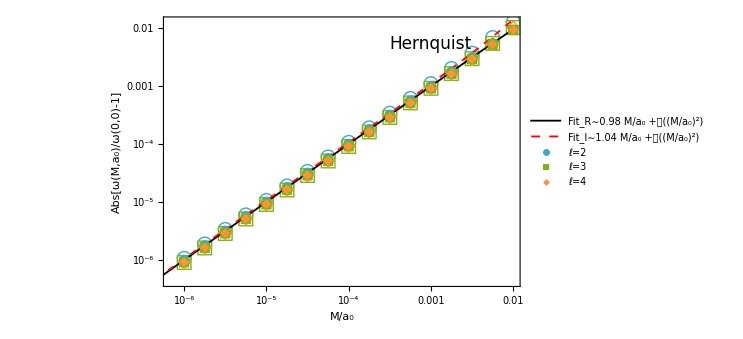

./plot/allZ_H_MM_fit.pdf

```mathematica
p1=ListLogLogPlot[{
datasetR[l2n0T,10^-2],
datasetR[l3n0T,10^-2],
datasetR[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",20],None},{Style["M/a_0",20],None}},PlotStyle->{Directive[Comb4[[3]],PointSize[0.8]],Directive[Comb1[[2]],PointSize[0.8]],Directive[Comb2[[2]],PointSize[0.8]]},PlotMarkers->{Automatic},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",16,FontFamily->"Palatino"],Style["ℓ=3",16,FontFamily->"Palatino"],Style["ℓ=4",16,FontFamily->"Palatino"]},Scaled[{0.1,0.85}]],ImageSize->550,ImagePadding->{{70, 50}, {70, 30}}];
p2=ListLogLogPlot[{
datasetI[l2n0T,10^-2],
datasetI[l3n0T,10^-2],
datasetI[l4n0T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",20],None},{Style["M/a_0",20],None}},PlotStyle->{Directive[Comb4[[3]],PointSize[0.8]],Directive[Comb1[[2]],PointSize[0.8]],Directive[Comb2[[2]],PointSize[0.8]]},PlotMarkers->{Style["○",FontSize->14],Style["□", FontSize->14],Style["◇",FontSize->13]},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->550,ImagePadding->{{70, 50}, {70, 30}},
Epilog->{leg["Hernquist",17,0,0.75,0.9,Black]}];
p3=LogLogPlot[{line2R, line2I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,AbsoluteThickness[1.3]],Directive[Red,Dashed,AbsoluteThickness[1.3]]},PlotLegends->Placed[{Style["Fit_R∼0.98 M/a_0 +𝒪((M/a_0)^2)",16,FontFamily->"Palatino"],Style["Fit_I∼1.04 M/a_0 +𝒪((M/a_0)^2)",16,FontFamily->"Palatino"]},Scaled[{0.7,0.25}]]];
p4=Show[p2,p3,p1]
Export["./plot/allZ_Hern_MM_fit.pdf",%]
```

### Extra (NFW)

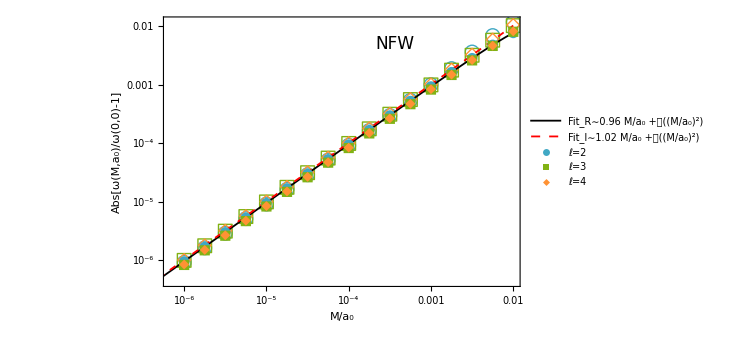

```mathematica
p1N=ListLogLogPlot[{
datasetR[dataNl2T,10^-2],
datasetR[dataNl3T,10^-2],
datasetR[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",20],None},{Style["M/a_0",20],None}},PlotStyle->{Directive[Comb4[[3]],PointSize[0.8]],Directive[Comb1[[2]],PointSize[0.8]],Directive[Comb2[[2]],PointSize[0.8]]},PlotMarkers->{Automatic},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],PlotLegends->Placed[{Style["ℓ=2",16,FontFamily->"Palatino"],Style["ℓ=3",16,FontFamily->"Palatino"],Style["ℓ=4",16,FontFamily->"Palatino"]},Scaled[{0.1,0.85}]],ImageSize->550,ImagePadding->{{70, 50}, {70, 30}}];
p2N=ListLogLogPlot[{
datasetI[dataNl2T,10^-2],
datasetI[dataNl3T,10^-2],
datasetI[dataNl4T,10^-2]},Frame->True,FrameLabel->{{Style["Abs[ω(M,a_0)/ω(0,0)-1]",20],None},{Style["M/a_0",20],None}},PlotStyle->{Directive[Comb4[[3]],PointSize[0.8]],Directive[Comb1[[2]],PointSize[0.8]],Directive[Comb2[[2]],PointSize[0.8]]},PlotMarkers->{Style["○",FontSize->14],Style["□", FontSize->14],Style["◇",FontSize->13]},FrameStyle->Directive[14,GrayLevel[0],FontFamily->"Palatino",AbsoluteThickness[1]],ImageSize->550,ImagePadding->{{70, 50}, {70, 30}},
Epilog->{leg["NFW",17,0,0.65,0.9,Black]}];
p3N=LogLogPlot[{lineN2R, lineN3I},{t,10^-7,0.01 },Frame->True,PlotRange->{{-0.001,0.101},{-0.001,0.101}},PlotStyle->{Directive[Black,AbsoluteThickness[1.3]],Directive[Red,Dashed,AbsoluteThickness[1.3]]},PlotLegends->Placed[{Style["Fit_R∼0.96 M/a_0 +𝒪((M/a_0)^2)",16,FontFamily->"Palatino"],Style["Fit_I∼1.02 M/a_0 +𝒪((M/a_0)^2)",16,FontFamily->"Palatino"]},Scaled[{0.7,0.25}]]];
p4N=Show[p2N,p3N,p1N]
Export["./plot/allZ_NFW_MM_fit.pdf",%]
```